```mathematica
Needs["MazeNavigation`"]
Needs["VisualizeGenome`"]
```

## Create Map

```mathematica
map1=Rasterize[Graphics[{Antialiasing->False,Black,Thickness[0.05],Line[{{1,1},{20,1},{20,20},{1,20},{1,1}}],
Line[{{1,5},{20,10}}],
Line[{{1,6},{20,11}}]
}],RasterSize->{20,20}];
map1=(map1/.Graphics->List)[[1,1]]/.{{0,0,0}->1,{255,255,255}->0};
map1[[4,2]]=2;
map1[[15,15]]=3;
```

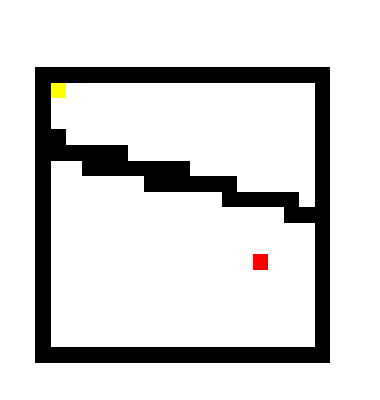

```mathematica
ArrayPlot[map1,ColorRules->{0->White,1->Black,2->Yellow,3->Red}]
```

```mathematica
Export["map1.csv",map1]
```

map1.csv

## Player

```mathematica
data=readAllFiles[{"GPAT_MAZE_MAP4_ORIG"}];
printAsTable[data,{"SOLVER"}]
expr=convertGPATGenome[sortConfigurationResults[data,"1","BSF",10,Output->"BSF"][[1,4]]]
```

ID | PARAM FILE | SOLVER
1 | GPAT_MAZE_MAP4_ORIG/parameters_001.txt | GPAT

{-ArcTan[3.10957+0.472039 x0-6.8829 x1+2.8946 x2-2.24012 x3+1.61314 x4+0.749032 x5-1.81171 x6]}

```mathematica
expr={Plus[-0.6469302754514258*x5]}
```

{-0.64693 x5}

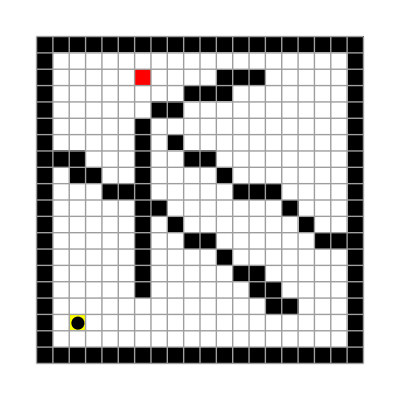

```mathematica
(state=loadMap["~/java/ne/cfg/demo/maze/map4.csv"])//showState
```

```mathematica
Manipulate[Nest[singleStep[#,expr]&,state,i]//showState,{i,0,100,1}]
```

```mathematica
data2=readAllFiles[{"GPAT_MAZE_MAP4_ORIG"}];
bestN=1;(*n-th best run*)
state2=loadMap["~/java/ne/cfg/demo/maze/map4.csv"];
printAsTable[data2,{"SOLVER"}]
expr2=
listBOGEvolution[Sequence@@(sortConfigurationResults[data2,"1","BSF",bestN,Output->"GenomeFileList"][[bestN]]),Choice->"Structural"];
Print[expr2//MatrixForm];
expr2=convertGPATGenome[expr2];
```

ID | PARAM FILE | SOLVER
1 | GPAT_MAZE_MAP4_ORIG/parameters_001.txt | GPAT

(1 | 100 | -1 | {plus} | 20.
2 | 153 | 16 | {plus[1.01262 x2]} | 30.
3 | 276 | 124 | {plus[0.797643 x2]} | 30.
4 | 340 | 228 | {plus[1.56049,-3.61071 x5]} | 31.
5 | 435 | 340 | {plus[1.55665,-3.61071 x5]} | 31.
6 | 587 | 434 | {plus[1.56049 x3,-4.03531 x5,0.991057 x2]} | 31.
7 | 678 | 587 | {plus[1.56049 x3,-4.03531 x5,0.991057 x2]} | 31.
8 | 768 | 678 | {plus[1.56049 x3,-4.03531 x5,0.991057 x2]} | 31.
9 | 860 | 766 | {plus[1.56049 x3,-4.03531 x5,0.991057 x2]} | 31.
10 | 946 | 860 | {plus[1.56049 x3,-4.03531 x5,0.0264272 x2]} | 31.
11 | 1083 | 991 | {sin[plus[1.52402 x3,-4.03531 x5,0.994972 x0]]} | 31.
12 | 1166 | 1077 | {plus[-1.97225 x5,-0.856513 x4,1. x2,1. x1]} | 31.
13 | 1283 | 1129 | {plus[-1.62486 x0,-3.3431 x5,1.00105]} | 31.
14 | 1379 | 1279 | {plus[-2.79504 x0,-3.29871 x5,1.]} | 31.
15 | 1444 | 1345 | {plus[-1.95905 x5,-4.11279 x4,1. x2,1.00774 x1]} | 31.
16 | 1577 | 1415 | {plus[-3.25821 x0,-3.29871 x5,1. x6]} | 31.
17 | 1669 | 1573 | {plus[-3.26265 x0,-3.29871 x5,1.]} | 31.
18 | 1770 | 1667 | {plus[-2.67944 x0,-3.29125 x5,1.02581,1. x6]} | 31.
19 | 1864 | 1766 | {plus[-3.26809 x0,-3.29125 x5,1.,1. x6]} | 31.
20 | 1964 | 1864 | {plus[-3.26809 x0,-4.19106 x5,1.,1. x1]} | 31.
21 | 2054 | 1937 | {plus[-3.26809 x4,-2.15372 x5,0.971115]} | 31.
22 | 2175 | 2053 | {plus[-3.26809 x0,-3.29871 x5,1.]} | 31.
23 | 2289 | 2122 | {plus[-3.35729,-4.61921 x5,4.11294 x6,0.913996 x4,3.56454 x0,2.38949 x3,-0.192594 x1]} | 31.
24 | 2302 | 2201 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
25 | 2401 | 2302 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
26 | 2504 | 2401 | {sin[plus[1.57534 x1,-3.61071 x5]]} | 36.
27 | 2605 | 2501 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
28 | 2701 | 2601 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
29 | 2801 | 2701 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
30 | 2906 | 2801 | {sin[plus[-3.89931 x1,-3.61071 x5]]} | 36.
31 | 3004 | 2901 | {sin[plus[1.56785 x1,-3.61288 x5]]} | 36.
32 | 3105 | 3001 | {sin[plus[1.62335 x1,-3.61092 x5]]} | 36.
33 | 3203 | 3101 | {sin[plus[1.56611 x1,-3.61071 x5]]} | 36.
34 | 3303 | 3201 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
35 | 3402 | 3301 | {sin[plus[1.12397 x1,-3.61071 x5]]} | 36.
36 | 3506 | 3401 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
37 | 3603 | 3501 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
38 | 3705 | 3601 | {sin[plus[1.57033 x1,-3.61071 x5]]} | 36.
39 | 3803 | 3701 | {sin[plus[1.59393 x1,-3.63564 x5]]} | 36.
40 | 3903 | 3801 | {sin[plus[1.56785 x1,-3.52876 x5]]} | 36.
41 | 4001 | 3901 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
42 | 4103 | 4001 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
43 | 4205 | 4101 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
44 | 4305 | 4201 | {sin[plus[1.56785 x1,-3.62463 x5]]} | 36.
45 | 4405 | 4301 | {sin[plus[1.56737 x1,-3.61071 x5]]} | 36.
46 | 4504 | 4401 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
47 | 4601 | 4501 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
48 | 4776 | 4601 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
49 | 4894 | 4776 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
50 | 4979 | 4890 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
51 | 5071 | 4974 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
52 | 5168 | 5069 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
53 | 5264 | 5168 | {sin[plus[1.57057 x1,-3.61071 x5]]} | 36.
54 | 5382 | 5261 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
55 | 5464 | 5377 | {sin[plus[1.49299 x1,-3.61071 x5]]} | 36.
56 | 5560 | 5461 | {sin[plus[1.56785 x1,-3.61847 x5]]} | 36.
57 | 5670 | 5555 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
58 | 5759 | 5665 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
59 | 5861 | 5756 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
60 | 5914 | 5861 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
61 | 6043 | 5901 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
62 | 6129 | 6033 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
63 | 6224 | 6123 | {sin[plus[-4.23129 x1,-3.57741 x5]]} | 36.
64 | 6318 | 6218 | {sin[plus[1.56785 x1,-3.61644 x5]]} | 36.
65 | 6480 | 6315 | {sin[plus[1.56245 x1,-3.61071 x5,1. x6]]} | 36.
66 | 6521 | 6415 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
67 | 6663 | 6517 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
68 | 6765 | 6659 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
69 | 6862 | 6762 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
70 | 6983 | 6862 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
71 | 7048 | 6978 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
72 | 7146 | 7045 | {sin[plus[1.56785 x1,-3.62015 x5]]} | 36.
73 | 7227 | 7141 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
74 | 7333 | 7227 | {sin[plus[1.56785 x1,-3.61071 x5],x6]} | 36.
75 | 7429 | 7329 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
76 | 7549 | 7428 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
77 | 7634 | 7549 | {sin[plus[-3.80199 x1,-3.61071 x5]]} | 36.
78 | 7730 | 7633 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
79 | 7826 | 7730 | {sin[plus[1.56785 x1,-3.60489 x5]]} | 36.
80 | 7930 | 7823 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
81 | 8029 | 7927 | {sin[plus[1.57465 x1,-3.61206 x5]]} | 36.
82 | 8127 | 8026 | {sin[plus[1.57601 x1,-3.61071 x5]]} | 36.
83 | 8227 | 8125 | {sin[plus[-4.2211 x1,-3.61071 x5]]} | 36.
84 | 8344 | 8225 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
85 | 8437 | 8337 | {sin[plus[-0.876974 x1,-3.61071 x6]]} | 36.
86 | 8530 | 8433 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
87 | 8645 | 8542 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
88 | 8743 | 8645 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
89 | 8842 | 8743 | {plus[-0.214288 x2,-0.0306729 x0,3.83034,-0.72389 x4,2.03945 x6,-2.60886 x5,-3.35013 x1]} | 36.
90 | 8940 | 8840 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
91 | 9058 | 8940 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
92 | 9165 | 9058 | {plus[-0.214273 x2,0.297186 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.5482 x1]} | 36.
93 | 9266 | 9164 | {plus[-0.214273 x2,0.303235 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
94 | 9346 | 9265 | {plus[-0.214273 x2,0.296298 x0,3.70587,-0.721426 x4,2.03945 x6,-2.64966 x5,-2.29134 x1]} | 36.
95 | 9454 | 9343 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
96 | 9558 | 9454 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
97 | 9673 | 9558 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
98 | 9764 | 9673 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
99 | 9866 | 9764 | {plus[-0.237231 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
100 | 9965 | 9865 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
101 | 10061 | 9965 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
102 | 10175 | 10061 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
103 | 10248 | 10175 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
104 | 10348 | 10248 | {plus[-0.210847 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.41611 x1]} | 36.
105 | 10441 | 10346 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
106 | 10557 | 10441 | {plus[-0.214273 x2,0.308483 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.389 x1]} | 36.
107 | 10642 | 10553 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
108 | 10741 | 10642 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
109 | 10824 | 10741 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
110 | 10929 | 10824 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
111 | 11027 | 10929 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.710361 x4,2.04334 x6,-2.60886 x5,-2.38579 x1]} | 36.
112 | 11138 | 11026 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
113 | 11230 | 11138 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
114 | 11333 | 11230 | {plus[-0.199808 x2,0.282339 x0,3.71324,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
115 | 11431 | 11329 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.37835 x1]} | 36.
116 | 11526 | 11426 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
117 | 11627 | 11526 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
118 | 11725 | 11627 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
119 | 11834 | 11725 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
120 | 11935 | 11834 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
121 | 12040 | 11935 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
122 | 12131 | 12035 | {plus[-0.495538 x2,0.299789 x0,3.70429,-0.737885 x4,2.0358 x6,-2.62492 x5,-2.38579 x1]} | 36.
123 | 12224 | 12128 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
124 | 12319 | 12224 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
125 | 12425 | 12319 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
126 | 12598 | 12410 | {plus[1. sin[plus[1.36365 x1,-3.61105 x5]]]} | 36.
127 | 12633 | 12527 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
128 | 12796 | 12615 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
129 | 12895 | 12790 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
130 | 12978 | 12822 | {sin[plus[-0.214273 x2,0.299789 x0,1.24893,-0.737885 x4,2.03193 x6,-0.742968 x5,-2.38579 x1]]} | 36.
131 | 13085 | 12978 | {sin[plus[-0.214273 x2,0.299789 x0,1.24893,-0.737885 x4,2.03193 x6,-0.742968 x5,-2.38579 x1]]} | 36.
132 | 13166 | 13085 | {sin[plus[-0.214273 x2,0.299789 x0,1.24893,-0.737885 x4,2.03193 x6,-0.742968 x5,-2.38579 x1]]} | 36.
133 | 13266 | 13166 | {sin[plus[-0.214273 x2,0.299789 x0,1.24893,-0.737885 x4,2.03193 x6,-0.742968 x5,-2.38579 x1]]} | 36.
134 | 13372 | 13266 | {sin[plus[-0.214273 x2,0.299789 x0,1.24893,-0.737885 x4,2.03193 x6,-0.742968 x5,-2.38579 x1]]} | 36.
135 | 13470 | 13372 | {sin[plus[-0.214273 x2,0.299789 x0,1.24893,-0.737885 x4,2.03193 x6,-0.742968 x5,-2.38579 x1]]} | 36.
136 | 13580 | 13459 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
137 | 13686 | 13517 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
138 | 13775 | 13681 | {plus[-0.214273 x2,0.297168 x0,3.70703,-0.708177 x4,2.03945 x6,-2.62787 x5,-2.38579 x1]} | 36.
139 | 13857 | 13774 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
140 | 13972 | 13857 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
141 | 14070 | 13972 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
142 | 14179 | 14068 | {plus[-0.214273 x2,0.285438 x0,3.71423,-0.737885 x4,1.64825 x6,-2.61518 x5,-2.38579 x1]} | 36.
143 | 14253 | 14177 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
144 | 14370 | 14253 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
145 | 14471 | 14335 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
146 | 14578 | 14471 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
147 | 14672 | 14578 | {sin[sin[plus[1.56785 x1,-3.61071 x5]]]} | 36.
148 | 14776 | 14669 | {sin[plus[1.56973 x1,-3.6234 x5]]} | 36.
149 | 14873 | 14772 | {sin[plus[-3.82915 x1,-3.60184 x5]]} | 36.
150 | 14989 | 14871 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
151 | 15073 | 14984 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
152 | 15178 | 15073 | {sin[plus[1.56785 x1,-3.61207 x5]]} | 36.
153 | 15261 | 15175 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
154 | 15369 | 15261 | {sin[plus[1.56785 x1,-3.60732 x5]]} | 36.
155 | 15472 | 15366 | {sin[plus[1.58297 x1,-3.61071 x5]]} | 36.
156 | 15564 | 15469 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
157 | 15666 | 15561 | {sin[plus[1.56785 x1,-3.61071 x5],x0]} | 36.
158 | 15771 | 15660 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
159 | 15863 | 15768 | {sin[plus[1.56785 x1,-3.61027 x5]]} | 36.
160 | 15982 | 15860 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
161 | 16064 | 15977 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
162 | 16167 | 16064 | {sin[plus[1.56785 x1,-3.61071 x5]]} | 36.
163 | 16288 | 16133 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
164 | 16387 | 16283 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
165 | 16498 | 16354 | {sin[plus[1.56532 x1,-3.61071 x5,1. x0]]} | 36.
166 | 16593 | 16482 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
167 | 16687 | 16561 | {sin[plus[1.56785 x1,-3.61422 x5]]} | 36.
168 | 16788 | 16673 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
169 | 16885 | 16782 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
170 | 16984 | 16881 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
171 | 17084 | 16979 | {sin[sin[x5,x1,x5,x1,x5]]} | 36.
172 | 17168 | 17078 | {atan[sin[x5,x0,x5,x1,x5]]} | 36.
173 | 17272 | 17166 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
174 | 17372 | 17268 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
175 | 17474 | 17367 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
176 | 17562 | 17469 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
177 | 17661 | 17560 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
178 | 17776 | 17661 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
179 | 17869 | 17771 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
180 | 17979 | 17865 | {atan[sin[x5,x0,x5,x1,x5]]} | 36.
181 | 18094 | 17942 | {plus[-0.214273 x2,-0.192296 x0,3.70703,-0.735548 x4,2.03945 x6,-2.60886 x5,-3.11075 x1]} | 36.
182 | 18186 | 18089 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
183 | 18283 | 18186 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
184 | 18383 | 18283 | {plus[-0.214273 x3,0.299789 x0,3.98642,-0.94608 x4,2.03945 x6,-2.60886 x5,-2.39261 x1]} | 36.
185 | 18485 | 18380 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.622259 x4,2.02872 x6,-2.61439 x5,-2.38222 x1]} | 36.
186 | 18587 | 18482 | {plus[-0.00447673 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.59756 x5,-2.38579 x1]} | 36.
187 | 18683 | 18584 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
188 | 18783 | 18683 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
189 | 18880 | 18783 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
190 | 18981 | 18880 | {plus[-0.214273 x2,0.299789 x0,3.71281,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.39445 x1]} | 36.
191 | 19084 | 18980 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,1.35993 x6,-2.60886 x5,-2.38579 x1]} | 36.
192 | 19175 | 19081 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
193 | 19275 | 19175 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
194 | 19389 | 19275 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
195 | 19490 | 19363 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
196 | 19590 | 19485 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
197 | 19670 | 19575 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
198 | 19776 | 19670 | {plus[-0.229565 x2,0.0350629 x0,3.71632,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
199 | 19883 | 19775 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
200 | 19986 | 19883 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
201 | 20084 | 19982 | {plus[-0.214273 x2,0.299789 x0,3.69369,-0.737885 x4,2.03945 x6,-2.60705 x5,-2.38579 x1]} | 36.
202 | 20186 | 20082 | {plus[-0.214273 x2,0.299789 x0,3.653,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.3911 x1]} | 36.
203 | 20284 | 20181 | {plus[-0.214849 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.59307 x5,-2.38579 x1]} | 36.
204 | 20377 | 20280 | {plus[-0.214273 x2,0.292998 x0,3.7082,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
205 | 20489 | 20375 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.31606 x1]} | 36.
206 | 20578 | 20486 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
207 | 20674 | 20578 | {plus[-0.219248 x2,0.299789 x0,3.70703,-0.7312 x4,2.03945 x6,-2.59273 x5,-4.36334 x1]} | 36.
208 | 20771 | 20672 | {plus[-0.214273 x2,-0.162477 x0,3.70703,-0.737885 x4,0.283625 x6,-2.92319 x5,-2.38579 x1,1. x3]} | 36.
209 | 20873 | 20768 | {plus[-0.303378 x2,-2.34356 x0,3.70703,-0.737885 x4,2.0443 x6,-2.60886 x5,-2.38579 x1]} | 36.
210 | 20968 | 20872 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
211 | 21079 | 20968 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
212 | 21178 | 21079 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
213 | 21281 | 21178 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
214 | 21355 | 21281 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
215 | 21465 | 21355 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
216 | 21564 | 21465 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.04024 x6,-2.60886 x5,-2.38579 x1]} | 36.
217 | 21661 | 21561 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
218 | 21764 | 21661 | {plus[-0.214273 x2,0.315816 x0,3.70703,-0.724435 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
219 | 21870 | 21763 | {plus[-0.211723 x2,0.306222 x3,3.70703,-0.737885 x4,2.04668 x6,-2.58834 x5,-2.38579 x1]} | 36.
220 | 21963 | 21868 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
221 | 22063 | 21963 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.55945 x5,-2.38579 x1]} | 36.
222 | 22163 | 22059 | {plus[-0.214273 x2,0.299789 x0,3.70852,-0.737885 x4,2.01808 x6,-2.60886 x5,-2.38579 x1]} | 36.
223 | 22266 | 22160 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
224 | 22359 | 22266 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
225 | 22456 | 22359 | {plus[-0.278288 x2,0.299789 x0,3.70703,-0.737885 x4,4.46674 x6,-2.60886 x5,-2.38579 x1]} | 36.
226 | 22568 | 22454 | {plus[-0.214273 x2,0.299789 x0,3.6396,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
227 | 22685 | 22505 | {plus[1.89303 x3,0.2266 x4,-2.62572 x1,-0.018401 x2,2.08569 x6,-4.54961 x5,4.38815,-4.54016 x0]} | 36.
228 | 22771 | 22682 | {plus[1.89303 x3,0.390043 x4,-2.6066 x1,-0.018401 x2,2.09728 x6,-4.54141 x5,4.38815,-4.54016 x0]} | 36.
229 | 22874 | 22771 | {plus[1.89303 x3,0.390043 x4,-2.6066 x1,-0.018401 x2,2.09728 x6,-4.54141 x5,4.38815,-4.54016 x0]} | 36.
230 | 22981 | 22870 | {plus[1.89303 x3,0.390043 x4,-2.6066 x1,-0.018401 x2,2.09728 x6,-4.54141 x5,4.38815,-4.54016 x0]} | 36.
231 | 23075 | 22981 | {plus[1.89303 x3,0.390043 x4,-2.6066 x1,-0.018401 x2,2.09728 x6,-4.54141 x5,4.38815,-4.54016 x0]} | 36.
232 | 23175 | 23075 | {plus[1.89303 x3,0.390043 x4,-2.6066 x1,-0.018401 x2,2.09728 x6,-4.54141 x5,4.38815,-4.54016 x0]} | 36.
233 | 23296 | 23145 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
234 | 23384 | 23290 | {atan[sin[x5,x0,x5,x1,x5]]} | 36.
235 | 23487 | 23380 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
236 | 23584 | 23484 | {times[sin[x5,x0,x5,x1,x5]]} | 36.
237 | 23699 | 23579 | {plus[1.0019 sin[x5,x0,x5,x1,x5]]} | 36.
238 | 23800 | 23695 | {atan[sin[x5,x0,x5,x1,x5]]} | 36.
239 | 23896 | 23795 | {sin[sin[x5,x1,x5,x1,x5]]} | 36.
240 | 23991 | 23892 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
241 | 24087 | 23986 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
242 | 24200 | 24083 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
243 | 24289 | 24194 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
244 | 24386 | 24283 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
245 | 24481 | 24383 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
246 | 24582 | 24476 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
247 | 24683 | 24578 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
248 | 24785 | 24679 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
249 | 24882 | 24780 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
250 | 24992 | 24878 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
251 | 25082 | 24904 | {sin[plus[1.56785 x1,-3.65318 x5,1.00774 x0]]} | 36.
252 | 25182 | 25080 | {sin[plus[1.56785 x1,-3.65318 x5,1. x0]]} | 36.
253 | 25285 | 25182 | {sin[plus[1.56785 x1,-3.65318 x5,1. x0]]} | 36.
254 | 25373 | 25280 | {sin[plus[1.56785 x1,-3.65318 x5,1. x0]]} | 36.
255 | 25454 | 25370 | {sin[plus[1.56785 x1,-3.65318 x5,1. x0]]} | 36.
256 | 25566 | 25470 | {plus[3.05892 sin[sin[x5,x0,x5,x1,x5]]]} | 36.
257 | 25661 | 25552 | {sin[plus[1.56785 x1,-3.6561 x5,1. x0]]} | 36.
258 | 25753 | 25658 | {sin[plus[1.56785 x1,-3.65318 x5,1. x0]]} | 36.
259 | 25858 | 25753 | {sin[plus[1.56112 x1,-3.65092 x5,0.994264 x0]]} | 36.
260 | 25967 | 25855 | {sin[plus[1.56785 x1,-3.65318 x5,1. x0]]} | 36.
261 | 26075 | 25919 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
262 | 26181 | 26075 | {plus[-0.215216 x2,0.299789 x0,3.70703,-0.737885 x4,0.352149 x6,-2.60886 x5,-2.38579 x1]} | 36.
263 | 26275 | 26179 | {plus[-0.235779 x2,0.322914 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
264 | 26349 | 26271 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
265 | 26494 | 26318 | {sin[sin[x5,times[x0],x5,x1,x5]]} | 36.
266 | 26592 | 26490 | {sin[sin[x5,times[x1],x5,x1,x5]]} | 36.
267 | 26671 | 26559 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
268 | 26788 | 26623 | {atan[sin[x5,x0,x5,x1,x5]]} | 36.
269 | 26889 | 26783 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
270 | 26984 | 26885 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
271 | 27081 | 26979 | {sin[sin[x5,x6,x5,x1,x5]]} | 36.
272 | 27177 | 27076 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
273 | 27270 | 27172 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
274 | 27378 | 27266 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
275 | 27491 | 27375 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
276 | 27579 | 27439 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
277 | 27686 | 27579 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.903087 x4,-1.92004 x0,2.28939,-3.86 x1]} | 36.
278 | 27773 | 27680 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
279 | 27871 | 27720 | {sin[plus[1.46019 x1,-3.65318 x5,-0.316645 x6]]} | 36.
280 | 27988 | 27870 | {sin[plus[2.00623 x1,-3.65318 x5,-0.348613 x0]]} | 36.
281 | 28075 | 27963 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
282 | 28180 | 28073 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
283 | 28255 | 28180 | {plus[-3.3399 x5,4.16146 x3,0.901369 x6,0.91628 x4,-1.90359 x0,2.28939 x2,-3.86 x1]} | 36.
284 | 28371 | 28253 | {plus[-3.35729 x5,4.16146 x3,2.48537 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-4.77296 x1]} | 36.
285 | 28459 | 28366 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
286 | 28567 | 28459 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
287 | 28688 | 28567 | {plus[-3.35808 x5,4.16146 x3,0.921505 x6,0.891627 x4,-1.93269 x0,2.28939 x2,-3.86 x1]} | 36.
288 | 28793 | 28641 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
289 | 28884 | 28793 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
290 | 28966 | 28884 | {atan[sin[x5,x0,x5,x1,x5]]} | 36.
291 | 29076 | 28963 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
292 | 29177 | 29080 | {plus[1.00314 sin[x5,x0,x5,x1,x5],1.11067 x6]} | 36.
293 | 29277 | 29166 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
294 | 29372 | 29277 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
295 | 29484 | 29372 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
296 | 29573 | 29484 | {plus[-3.35729 x5,4.13281 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
297 | 29691 | 29547 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0],x4]} | 36.
298 | 29764 | 29656 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,1.47918 x4,-1.92004 x0,2.31733 x2,-3.86 x1]} | 36.
299 | 29878 | 29738 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
300 | 29991 | 29878 | {sin[plus[2.13894 x1,-3.65318 x5,-0.348613 x0]]} | 36.
301 | 30086 | 29991 | {sin[plus[2.13894 x1,-3.65318 x5,-0.348613 x0]]} | 36.
302 | 30181 | 30081 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
303 | 30281 | 30181 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
304 | 30382 | 30281 | {sin[plus[2.01295 x1,-3.64734 x5,-0.348613 x0]]} | 36.
305 | 30495 | 30378 | {sin[plus[2.01295 x1,-3.65318 x5,-0.358277 x0]]} | 36.
306 | 30577 | 30489 | {sin[plus[2.01295 x1,-3.65318 x5,0.567521 x0]]} | 36.
307 | 30678 | 30573 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
308 | 30772 | 30675 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
309 | 30886 | 30769 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
310 | 30992 | 30858 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
311 | 31091 | 30992 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
312 | 31182 | 31087 | {atan[sin[x5,x0,x5,x1,x5],x6]} | 36.
313 | 31276 | 31170 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.29099 x2,-3.86 x1]} | 36.
314 | 31377 | 31273 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
315 | 31490 | 31377 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
316 | 31583 | 31490 | {plus[-3.35729 x5,4.15622 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
317 | 31674 | 31581 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
318 | 31778 | 31674 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.29098 x2,-3.86 x1]} | 36.
319 | 31880 | 31776 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
320 | 31981 | 31880 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
321 | 32077 | 31981 | {plus[-3.35729 x5,4.19283 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
322 | 32170 | 32075 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
323 | 32286 | 32170 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
324 | 32375 | 32286 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
325 | 32472 | 32375 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
326 | 32568 | 32472 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.89738 x0,2.28939 x2,-3.86 x1]} | 36.
327 | 32677 | 32565 | {plus[-3.35729 x5,4.16146 x3,0.891741 x6,0.891627 x4,-1.92004 x0,2.29477 x2,-3.86 x1]} | 36.
328 | 32758 | 32672 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
329 | 32864 | 32758 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
330 | 32968 | 32864 | {plus[-3.35729 x5,4.1708 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
331 | 33076 | 32964 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
332 | 33195 | 33042 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
333 | 33297 | 33195 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
334 | 33368 | 33297 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
335 | 33487 | 33368 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
336 | 33583 | 33487 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
337 | 33673 | 33559 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
338 | 33780 | 33639 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
339 | 33880 | 33780 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
340 | 33994 | 33880 | {plus[-0.204645 x2,-0.602205 x0,3.70703,-0.737885 x4,2.03413 x6,-2.60171 x5,-2.41558 x1]} | 36.
341 | 34084 | 33991 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
342 | 34185 | 34084 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
343 | 34281 | 34185 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
344 | 34395 | 34281 | {plus[-0.129102 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-3.38693 x5,-2.38163 x1]} | 36.
345 | 34484 | 34392 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
346 | 34585 | 34484 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
347 | 34686 | 34543 | {sin[plus[2.01295 x1,-3.65318 x5,0.45812 x0]]} | 36.
348 | 34779 | 34684 | {sin[plus[2.01295 x1,-3.65318 x5,-0.164034 x0]]} | 36.
349 | 34896 | 34777 | {sin[plus[2.01295 x1,-3.65318 x5,-0.347088 x0]]} | 36.
350 | 34971 | 34891 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
351 | 35091 | 34971 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
352 | 35183 | 35088 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
353 | 35276 | 35179 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
354 | 35390 | 35273 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
355 | 35474 | 35385 | {sin[plus[2.01446 x1,-3.6458 x5,0.243644 x0]]} | 36.
356 | 35559 | 35470 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
357 | 35671 | 35558 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
358 | 35764 | 35671 | {sin[plus[2.01295 x1,-3.65666 x5,-0.348613 x0]]} | 36.
359 | 35863 | 35760 | {sin[plus[2.00095 x1,-3.65511 x5,-0.348613 x0]]} | 36.
360 | 35967 | 35859 | {sin[plus[2.87624 x1,-3.65318 x5,-0.348613 x6]]} | 36.
361 | 36070 | 35964 | {sin[plus[2.01124 x1,-3.65318 x5,-0.343766 x0]]} | 36.
362 | 36163 | 36066 | {sin[plus[2.01472 x1,-3.65318 x5,-0.360366 x0]]} | 36.
363 | 36261 | 36160 | {sin[plus[2.02766 x1,-3.65318 x5,-0.348613 x6]]} | 36.
364 | 36372 | 36260 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
365 | 36474 | 36369 | {sin[plus[2.01295 x1,2.75826 x5,-0.348613 x0]]} | 36.
366 | 36569 | 36467 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
367 | 36658 | 36566 | {sin[plus[2.01295 x1,-2.64103 x5,-0.348613 x0]]} | 36.
368 | 36760 | 36655 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
369 | 36861 | 36756 | {sin[plus[2.03054 x1,-3.65318 x5,-0.348613 x0]]} | 36.
370 | 36971 | 36858 | {sin[plus[2.01295 x1,-3.65897 x5,-0.348613 x0]]} | 36.
371 | 37067 | 36965 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
372 | 37170 | 37066 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
373 | 37282 | 37139 | {plus[-4.28913 x5,4.15677 x3,0.897731 x6,0.891627 x4,-1.03863 x0,2.28939 x2,-3.86 x1,0.962782]} | 36.
374 | 37364 | 37252 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
375 | 37455 | 37364 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
376 | 37563 | 37455 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
377 | 37664 | 37563 | {sin[plus[2.01295 x1,-3.46408 x5,-0.348613 x0]]} | 36.
378 | 37795 | 37628 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
379 | 37893 | 37790 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
380 | 37978 | 37889 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
381 | 38087 | 37974 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
382 | 38183 | 38083 | {times[sin[x5,x0,x5,x1,x5]]} | 36.
383 | 38278 | 38179 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
384 | 38391 | 38275 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
385 | 38476 | 38386 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
386 | 38574 | 38472 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
387 | 38680 | 38569 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
388 | 38777 | 38673 | {sin[sin[x5,x0,atan[x5],x1,x5]]} | 36.
389 | 38889 | 38777 | {sin[sin[x5,x0,atan[x5],x1,x5]]} | 36.
390 | 39000 | 38887 | {atan[sin[x5,x0,atan[x5],x1,x5]]} | 36.
391 | 39083 | 38974 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
392 | 39191 | 39077 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
393 | 39300 | 39185 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
394 | 39389 | 39296 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
395 | 39481 | 39386 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
396 | 39583 | 39480 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
397 | 39676 | 39579 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
398 | 39790 | 39672 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
399 | 39882 | 39785 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
400 | 39982 | 39877 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
401 | 40074 | 39977 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
402 | 40184 | 40070 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
403 | 40266 | 40179 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
404 | 40376 | 40261 | {plus[1.0019 sin[x5,x0,x5,x1,x5]]} | 36.
405 | 40475 | 40372 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
406 | 40570 | 40469 | {plus[1.0019 sin[x5,x0,x5,x1,x5]]} | 36.
407 | 40664 | 40568 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
408 | 40765 | 40662 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
409 | 40878 | 40762 | {atan[sin[x5,x0,x5,x1,x5]]} | 36.
410 | 40979 | 40875 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
411 | 41072 | 40973 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
412 | 41169 | 41069 | {times[sin[x5,x0,x5,x1,x5]]} | 36.
413 | 41269 | 41166 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
414 | 41364 | 41264 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
415 | 41477 | 41359 | {times[sin[x5,x0,x5,x1,x5]]} | 36.
416 | 41564 | 41472 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
417 | 41665 | 41558 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
418 | 41756 | 41660 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
419 | 41867 | 41751 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
420 | 41972 | 41862 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
421 | 42075 | 41969 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
422 | 42173 | 42071 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
423 | 42288 | 42170 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
424 | 42380 | 42283 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
425 | 42476 | 42375 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
426 | 42568 | 42471 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
427 | 42673 | 42562 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
428 | 42783 | 42633 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
429 | 42859 | 42754 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
430 | 42963 | 42854 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
431 | 43068 | 42958 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
432 | 43156 | 43065 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
433 | 43259 | 43152 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
434 | 43350 | 43255 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
435 | 43454 | 43347 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
436 | 43556 | 43451 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
437 | 43651 | 43551 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
438 | 43770 | 43648 | {sin[sin[x5,x1,x5,x1,x5]]} | 36.
439 | 43878 | 43724 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
440 | 43974 | 43878 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
441 | 44064 | 43974 | {plus[-3.98168 x5,4.16146 x3,0.897731 x6,1.61086 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
442 | 44172 | 44062 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
443 | 44255 | 44172 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
444 | 44357 | 44255 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
445 | 44470 | 44357 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
446 | 44552 | 44470 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
447 | 44654 | 44552 | {plus[-3.35729 x5,4.16146 x3,0.883823 x6,0.891627 x4,-1.92025 x0,2.28939 x2,-4.21756 x1]} | 36.
448 | 44765 | 44653 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.9421 x0,2.28939 x2,-3.86 x1]} | 36.
449 | 44854 | 44763 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
450 | 44951 | 44854 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.899377 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
451 | 45047 | 44949 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
452 | 45148 | 45047 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
453 | 45259 | 45148 | {plus[-3.35729 x5,4.16146 x3,3.72157 x6,0.893232 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
454 | 45357 | 45258 | {plus[1. plus[-3.35729 x5,4.16146 x3,0.904977 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]]} | 36.
455 | 45447 | 45352 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
456 | 45588 | 45447 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
457 | 45700 | 45588 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
458 | 45781 | 45696 | {plus[-3.35671 x5,4.40558 x3,0.907741 x6,0.896536 x4,-1.93706 x0,2.26032 x2,-3.85588 x1]} | 36.
459 | 45866 | 45777 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
460 | 45980 | 45866 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
461 | 46082 | 45980 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
462 | 46189 | 46082 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
463 | 46279 | 46185 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
464 | 46383 | 46279 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
465 | 46493 | 46383 | {plus[-3.36715 x5,4.16146 x3,2.93764 x6,0.891627 x4,-4.15346 x0,2.28939 x2,-3.86 x1]} | 36.
466 | 46587 | 46491 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
467 | 46683 | 46587 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
468 | 46780 | 46683 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
469 | 46873 | 46780 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
470 | 46987 | 46873 | {plus[-3.36832 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.71257 x1]} | 36.
471 | 47075 | 46985 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
472 | 47171 | 47075 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
473 | 47284 | 47171 | {plus[-3.34274 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
474 | 47373 | 47280 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
475 | 47486 | 47373 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.5511 x2,-3.86 x1]} | 36.
476 | 47572 | 47482 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
477 | 47675 | 47572 | {plus[-3.35729 x5,4.16273 x3,2.18625 x6,0.804339 x4,-1.92004 x0,2.25253 x2,-3.86 x1]} | 36.
478 | 47759 | 47674 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
479 | 47873 | 47759 | {plus[-3.35729 x5,4.16146 x3,3.69765 x6,0.891627 x4,-1.92004 x0,2.27366 x2,-3.86 x1]} | 36.
480 | 47974 | 47872 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.878215 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
481 | 48068 | 47970 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
482 | 48172 | 48068 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
483 | 48273 | 48172 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.891627 x4,-1.92004 x0,2.28939 x2,-3.86 x1]} | 36.
484 | 48392 | 48217 | {sin[plus[2.01295 x1,-3.65318 x5,-0.956536 x0]]} | 36.
485 | 48492 | 48391 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
486 | 48586 | 48488 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
487 | 48695 | 48586 | {sin[plus[1.98123 x1,-3.65318 x5,-0.348613 x0]]} | 36.
488 | 48792 | 48691 | {sin[plus[2.01898 x1,-3.65318 x5,-0.348613 x0]]} | 36.
489 | 48895 | 48791 | {sin[plus[2.03022 x1,3.59171 x5,-0.340836 x0]]} | 36.
490 | 48991 | 48891 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
491 | 49094 | 48991 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
492 | 49193 | 49091 | {sin[plus[2.01295 x1,-3.65318 x5,-0.38154 x0]]} | 36.
493 | 49296 | 49189 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
494 | 49395 | 49292 | {sin[plus[2.02002 x1,-3.65318 x5,-0.348613 x0]]} | 36.
495 | 49490 | 49390 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
496 | 49595 | 49490 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
497 | 49692 | 49593 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
498 | 49791 | 49691 | {sin[plus[2.01295 x1,3.29728 x5,-0.348613 x0]]} | 36.
499 | 49892 | 49790 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
500 | 49992 | 49890 | {sin[plus[2.01295 x1,-3.65318 x5,-0.755025 x0]]} | 36.
501 | 50095 | 49989 | {sin[plus[2.01295 x1,-3.63656 x5,-0.348613 x0]]} | 36.
502 | 50191 | 50091 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
503 | 50294 | 50190 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
504 | 50387 | 50289 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
505 | 50491 | 50383 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
506 | 50589 | 50486 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
507 | 50691 | 50584 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
508 | 50785 | 50687 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
509 | 50887 | 50785 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
510 | 50987 | 50887 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
511 | 51087 | 50987 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
512 | 51184 | 51086 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
513 | 51286 | 51184 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
514 | 51386 | 51285 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
515 | 51491 | 51386 | {sin[plus[1.96612 x1,-3.65318 x5,-0.348613 x0]]} | 36.
516 | 51585 | 51488 | {sin[plus[2.01295 x1,-3.65318 x5,-0.342091 x0]]} | 36.
517 | 51683 | 51558 | {plus[-3.35729 x5,4.16146 x3,0.897731 x6,0.89974 x4,-1.91516 x0,2.28939 x2,-3.86 x1]} | 36.
518 | 51777 | 51658 | {sin[times[x2,x4,x5,x1,x5,x6,x0],x1,x5,1,x5]} | 36.
519 | 51882 | 51771 | {sin[times[x2,x4,x3,x1,x5,x6,x0],x1,x5,1,x5]} | 36.
520 | 51973 | 51874 | {sin[times[x2,x4,x5,x1,x5,x6,x0],x1,x5,1,x5]} | 36.
521 | 52081 | 51963 | {sin[plus[2.02453 x1,-3.65318 x5,-0.380906 x0],x4]} | 36.
522 | 52170 | 52049 | {sin[times[x2,x4,x5,x1,x5,x6,x0],x1,x5,1,x5]} | 36.
523 | 52277 | 52162 | {sin[plus[2.01295 x1,-3.65318 x5,-0.380742 x0],x4]} | 36.
524 | 52387 | 52271 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
525 | 52479 | 52384 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
526 | 52583 | 52479 | {sin[plus[2.01869 x1,-3.65318 x5,-0.335509 x0]]} | 36.
527 | 52690 | 52580 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
528 | 52774 | 52630 | {times[plus[-0.969604 plus[-0.835377 x2,1.72973 x4,0.38609 x5,1.01348 x1,0.454934 x3,-2.15223 x6,-1.73103 x0,-1.70929],-3.13114 x1]]} | 36.
529 | 52877 | 52774 | {times[plus[-0.969604 plus[-0.835377 x2,1.72973 x4,0.38609 x5,1.01348 x1,0.454934 x3,-2.15223 x6,-1.73103 x0,-1.70929],-3.13114 x1]]} | 36.
530 | 52988 | 52819 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
531 | 53092 | 52984 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
532 | 53187 | 53088 | {sin[sin[x5,x1,x5,x1,x5]]} | 36.
533 | 53300 | 53182 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
534 | 53378 | 53294 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
535 | 53476 | 53373 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
536 | 53573 | 53470 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
537 | 53668 | 53570 | {times[sin[x5,x0,x5,x1,x5]]} | 36.
538 | 53787 | 53663 | {sin[sin[x5,x0,x5,x1,x5]]} | 36.
539 | 53885 | 53724 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
540 | 53979 | 53885 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
541 | 54091 | 53941 | {sin[plus[2.01295 x1,-3.64391 x5,0.159401 x0]]} | 36.
542 | 54180 | 54086 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
543 | 54285 | 54177 | {sin[plus[2.01295 x1,-3.65318 x5,-0.336836 x0]]} | 36.
544 | 54378 | 54284 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
545 | 54485 | 54375 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
546 | 54600 | 54482 | {sin[plus[2.05515 x1,-3.65318 x5,-0.348613 x0]]} | 36.
547 | 54687 | 54594 | {sin[plus[2.01926 x1,-3.65318 x5,-0.348613 x0]]} | 36.
548 | 54778 | 54682 | {sin[plus[2.01295 x1,-3.65318 x5,-0.328429 x0]]} | 36.
549 | 54861 | 54776 | {sin[plus[2.01295 x1,-3.65318 x5,-0.348613 x0]]} | 36.
550 | 54971 | 54860 | {sin[plus[2.08543 x1,-3.65318 x5,-0.348613 x0]]} | 36.
551 | 55069 | 54970 | {sin[plus[2.00293 x1,-3.65318 x5,-0.352811 x0]]} | 36.
552 | 55166 | 55065 | {sin[plus[2.01295 x1,-3.63738 x5,-0.352615 x0]]} | 36.
553 | 55284 | 55164 | {sin[plus[2.01295 x1,-3.65318 x5,-0.355156 x0]]} | 36.
554 | 55379 | 55270 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
555 | 55481 | 55379 | {plus[-0.214273 x2,-0.862841 x0,3.71302,-0.737885 x4,2.03945 x6,-3.08063 x5,-2.38579 x1]} | 36.
556 | 55579 | 55478 | {plus[-0.223169 x2,0.299789 x0,3.70278,-0.728017 x4,2.04431 x6,-2.60886 x5,-2.38579 x1]} | 36.
557 | 55668 | 55576 | {plus[-0.214273 x2,0.410203 x0,3.73155,-0.737885 x4,-0.36361 x6,-2.60853 x5,-2.38579 x1]} | 36.
558 | 55765 | 55665 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
559 | 55857 | 55765 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
560 | 55971 | 55857 | {plus[-0.214273 x2,-1.45039 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38648 x1]} | 36.
561 | 56079 | 55970 | {plus[-0.214273 x2,0.279879 x0,3.70703,-0.802376 x4,1.99192 x6,-3.24156 x5,-2.37652 x1]} | 36.
562 | 56162 | 56074 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
563 | 56273 | 56162 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
564 | 56373 | 56273 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
565 | 56489 | 56373 | {plus[-0.214273 x2,0.299202 x0,3.70226,-0.737885 x4,2.03945 x6,-2.62284 x5,-2.38578 x1]} | 36.
566 | 56581 | 56484 | {plus[-0.214273 x2,0.302428 x0,3.70975,-0.713385 x4,1.9867 x6,-2.60886 x5,-2.35687 x1]} | 36.
567 | 56680 | 56576 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
568 | 56775 | 56680 | {plus[-0.214273 x2,0.288607 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
569 | 56867 | 56774 | {plus[-0.214273 x2,0.303974 x0,3.70703,-0.737885 x4,2.03945 x6,-2.6236 x5,-2.38579 x1]} | 36.
570 | 56960 | 56865 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
571 | 57065 | 56960 | {plus[-0.214273 x2,0.279114 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
572 | 57158 | 57062 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
573 | 57276 | 57158 | {plus[-0.214273 x2,0.299789 x0,3.70703,-0.737885 x4,2.03945 x6,-2.60886 x5,-2.38579 x1]} | 36.
574 | 57385 | 57263 | {atan[plus[3.26471 plus[0.751668 x2,2.36453 x4,-2.87801 x0,-3.02327 x1,2.5096 x3,3.43164 x6,-1.40851],-3.60572 x4,3.10075 x3,1. x0]]} | 36.
575 | 57487 | 57385 | {atan[plus[3.26471 plus[0.751668 x2,2.36453 x4,-2.87801 x0,-3.02327 x1,2.5096 x3,3.43164 x6,-1.40851],-3.60572 x4,3.10075 x3,1. x0]]} | 36.
576 | 57587 | 57487 | {atan[plus[3.26471 plus[0.751668 x2,2.36453 x4,-2.87801 x0,-3.02327 x1,2.5096 x3,3.43164 x6,-1.40851],-3.60572 x4,3.10075 x3,1. x0]]} | 36.
577 | 57684 | 57587 | {atan[plus[3.26471 plus[0.751668 x2,2.36453 x4,-2.87801 x0,-3.02327 x1,2.5096 x3,3.43164 x6,-1.40851],-3.60572 x4,3.10075 x3,1. x0]]} | 36.
578 | 57792 | 57681 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
579 | 57876 | 57792 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
580 | 57970 | 57876 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
581 | 58065 | 57970 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
582 | 58180 | 58065 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
583 | 58269 | 58180 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
584 | 58360 | 58269 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
585 | 58465 | 58360 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
586 | 58564 | 58465 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
587 | 58651 | 58564 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
588 | 58755 | 58651 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
589 | 58853 | 58755 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
590 | 58963 | 58853 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
591 | 59063 | 58963 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.687401 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.8605 x6],x1,x4,x5]} | 38.
592 | 59171 | 59062 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
593 | 59265 | 59171 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
594 | 59363 | 59265 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
595 | 59459 | 59363 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
596 | 59556 | 59459 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
597 | 59666 | 59556 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.686822 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
598 | 59753 | 59664 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
599 | 59855 | 59753 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
600 | 59954 | 59855 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
601 | 60053 | 59954 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
602 | 60162 | 60053 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
603 | 60260 | 60162 | {atan[plus[-2.86407 x2,-2.57063 x4,-0.694471 x5,5.45056 x1,2.24012 x3,-3.12012,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
604 | 60349 | 60255 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
605 | 60453 | 60349 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
606 | 60550 | 60453 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
607 | 60649 | 60550 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
608 | 60758 | 60649 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
609 | 60858 | 60758 | {atan[plus[-2.8946 x2,-2.71433 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10983,-0.411477 x0,1.8147 x6],x1,x4,x5]} | 38.
610 | 60961 | 60855 | {atan[plus[-2.90152 x2,-1.54522 x4,-0.694471 x5,4.8829 x1,2.23892 x3,-3.11157,-0.472039 x0,1.78276 x6],x1,x4,x5]} | 38.
611 | 61049 | 60956 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
612 | 61153 | 61049 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
613 | 61245 | 61153 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
614 | 61358 | 61245 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
615 | 61449 | 61358 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
616 | 61553 | 61449 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
617 | 61650 | 61553 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
618 | 61751 | 61650 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
619 | 61852 | 61751 | {atan[plus[-2.8946 x2,-2.55405 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
620 | 61947 | 61849 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
621 | 62055 | 61947 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
622 | 62148 | 62055 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
623 | 62254 | 62148 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
624 | 62359 | 62254 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.18654,-0.509504 x0,1.81171 x6],x1,x4,x5]} | 38.
625 | 62453 | 62356 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
626 | 62542 | 62453 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
627 | 62647 | 62542 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
628 | 62745 | 62647 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
629 | 62848 | 62745 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
630 | 62948 | 62848 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
631 | 63050 | 62948 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
632 | 63148 | 63050 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.80976 x6],x1,x4,x5]} | 38.
633 | 63248 | 63147 | {atan[plus[-2.12981 x2,-2.57538 x4,-0.699875 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
634 | 63346 | 63246 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
635 | 63450 | 63346 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
636 | 63542 | 63446 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
637 | 63655 | 63542 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24112 x3,-3.10957,-0.469764 x0,1.81171 x6],x1,x1,x5]} | 38.
638 | 63751 | 63652 | {atan[plus[-2.8946 x2,-2.61314 x4,-0.749032 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x1]} | 40.)

```mathematica
{1,14,15,22,24,33,37,38}
```

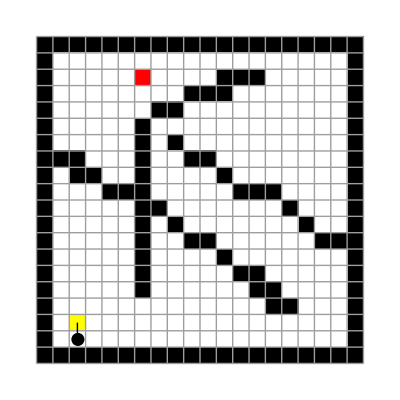
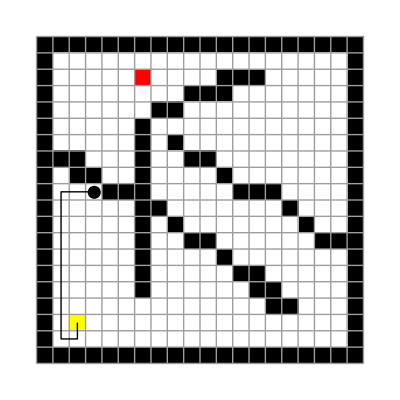
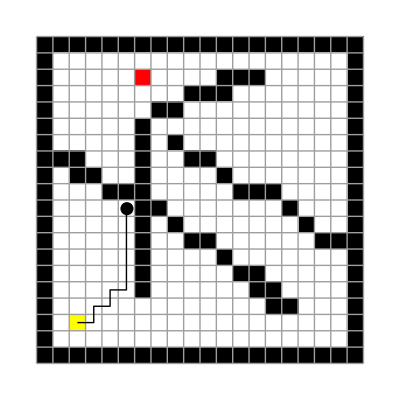
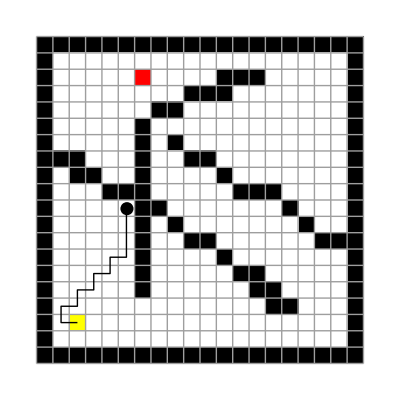
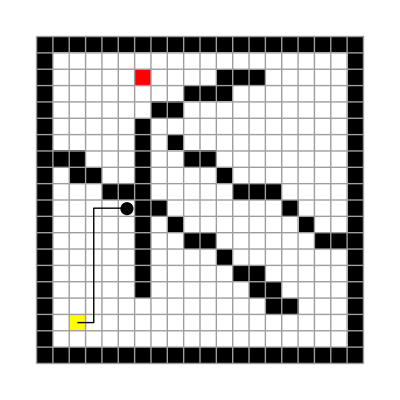
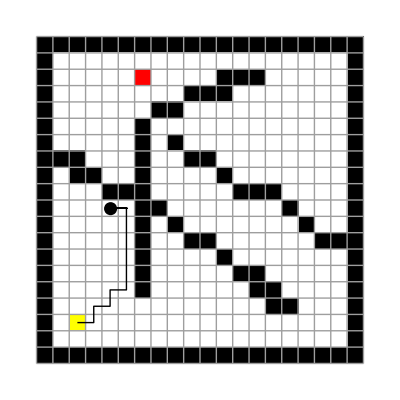
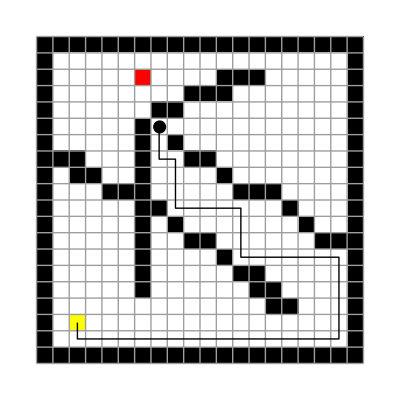
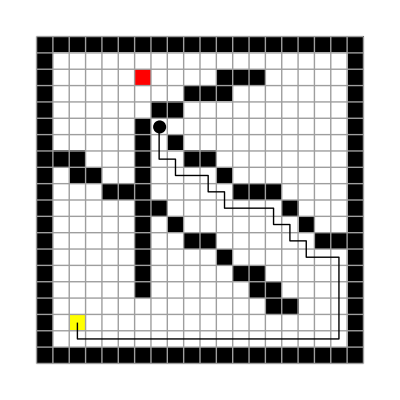
{-Graphics-
Generation 1
f = 20.,-Graphics-
Generation 2
f = 30.,-Graphics-
Generation 3
f = 30.,-Graphics-
Generation 4
f = 31.,-Graphics-
Generation 5
f = 31.,-Graphics-
Generation 6
f = 31.,-Graphics-
Generation 7
f = 31.,-Graphics-
Generation 8
f = 31.,-Graphics-
Generation 9
f = 31.,-Graphics-
Generation 10
f = 31.,-Graphics-
Generation 11
f = 31.,-Graphics-
Generation 12
f = 31.,-Graphics-
Generation 13
f = 31.,-Graphics-
Generation 14
f = 31.,-Graphics-
Generation 15
f = 31.,-Graphics-
Generation 16
f = 31.,-Graphics-
Generation 17
f = 31.,-Graphics-
Generation 18
f = 31.,-Graphics-
Generation 19
f = 31.,-Graphics-
Generation 20
f = 31.,-Graphics-
Generation 21
f = 31.,-Graphics-
Generation 22
f = 31.,-Graphics-
Generation 23
f = 31.,-Graphics-
Generation 24
f = 36.,-Graphics-
Generation 25
f = 36.,-Graphics-
Generation 26
f = 36.,-Graphics-
Generation 27
f = 36.,-Graphics-
Generation 28
f = 36.,-Graphics-
Generation 29
f = 36.,-Graphics-
Generation 30
f = 36.,-Graphics-
Generation 31
f = 36.,-Graphics-
Generation 32
f = 36.,-Graphics-
Generation 33
f = 36.,-Graphics-
Generation 34
f = 36.,-Graphics-
Generation 35
f = 36.,-Graphics-
Generation 36
f = 36.,-Graphics-
Generation 37
f = 36.,-Graphics-
Generation 38
f = 36.,-Graphics-
Generation 39
f = 36.,-Graphics-
Generation 40
f = 36.,-Graphics-
Generation 41
f = 36.,-Graphics-
Generation 42
f = 36.,-Graphics-
Generation 43
f = 36.,-Graphics-
Generation 44
f = 36.,-Graphics-
Generation 45
f = 36.,-Graphics-
Generation 46
f = 36.,-Graphics-
Generation 47
f = 36.,-Graphics-
Generation 48
f = 36.,-Graphics-
Generation 49
f = 36.,-Graphics-
Generation 50
f = 36.,-Graphics-
Generation 51
f = 36.,-Graphics-
Generation 52
f = 36.,-Graphics-
Generation 53
f = 36.,-Graphics-
Generation 54
f = 36.,-Graphics-
Generation 55
f = 36.,-Graphics-
Generation 56
f = 36.,-Graphics-
Generation 57
f = 36.,-Graphics-
Generation 58
f = 36.,-Graphics-
Generation 59
f = 36.,-Graphics-
Generation 60
f = 36.,-Graphics-
Generation 61
f = 36.,-Graphics-
Generation 62
f = 36.,-Graphics-
Generation 63
f = 36.,-Graphics-
Generation 64
f = 36.,-Graphics-
Generation 65
f = 36.,-Graphics-
Generation 66
f = 36.,-Graphics-
Generation 67
f = 36.,-Graphics-
Generation 68
f = 36.,-Graphics-
Generation 69
f = 36.,-Graphics-
Generation 70
f = 36.,-Graphics-
Generation 71
f = 36.,-Graphics-
Generation 72
f = 36.,-Graphics-
Generation 73
f = 36.,-Graphics-
Generation 74
f = 36.,-Graphics-
Generation 75
f = 36.,-Graphics-
Generation 76
f = 36.,-Graphics-
Generation 77
f = 36.,-Graphics-
Generation 78
f = 36.,-Graphics-
Generation 79
f = 36.,-Graphics-
Generation 80
f = 36.,-Graphics-
Generation 81
f = 36.,-Graphics-
Generation 82
f = 36.,-Graphics-
Generation 83
f = 36.,-Graphics-
Generation 84
f = 36.,-Graphics-
Generation 85
f = 36.,-Graphics-
Generation 86
f = 36.,-Graphics-
Generation 87
f = 36.,-Graphics-
Generation 88
f = 36.,-Graphics-
Generation 89
f = 36.,-Graphics-
Generation 90
f = 36.,-Graphics-
Generation 91
f = 36.,-Graphics-
Generation 92
f = 36.,-Graphics-
Generation 93
f = 36.,-Graphics-
Generation 94
f = 36.,-Graphics-
Generation 95
f = 36.,-Graphics-
Generation 96
f = 36.,-Graphics-
Generation 97
f = 36.,-Graphics-
Generation 98
f = 36.,-Graphics-
Generation 99
f = 36.,-Graphics-
Generation 100
f = 36.,-Graphics-
Generation 101
f = 36.,-Graphics-
Generation 102
f = 36.,-Graphics-
Generation 103
f = 36.,-Graphics-
Generation 104
f = 36.,-Graphics-
Generation 105
f = 36.,-Graphics-
Generation 106
f = 36.,-Graphics-
Generation 107
f = 36.,-Graphics-
Generation 108
f = 36.,-Graphics-
Generation 109
f = 36.,-Graphics-
Generation 110
f = 36.,-Graphics-
Generation 111
f = 36.,-Graphics-
Generation 112
f = 36.,-Graphics-
Generation 113
f = 36.,-Graphics-
Generation 114
f = 36.,-Graphics-
Generation 115
f = 36.,-Graphics-
Generation 116
f = 36.,-Graphics-
Generation 117
f = 36.,-Graphics-
Generation 118
f = 36.,-Graphics-
Generation 119
f = 36.,-Graphics-
Generation 120
f = 36.,-Graphics-
Generation 121
f = 36.,-Graphics-
Generation 122
f = 36.,-Graphics-
Generation 123
f = 36.,-Graphics-
Generation 124
f = 36.,-Graphics-
Generation 125
f = 36.,-Graphics-
Generation 126
f = 36.,-Graphics-
Generation 127
f = 36.,-Graphics-
Generation 128
f = 36.,-Graphics-
Generation 129
f = 36.,-Graphics-
Generation 130
f = 36.,-Graphics-
Generation 131
f = 36.,-Graphics-
Generation 132
f = 36.,-Graphics-
Generation 133
f = 36.,-Graphics-
Generation 134
f = 36.,-Graphics-
Generation 135
f = 36.,-Graphics-
Generation 136
f = 36.,-Graphics-
Generation 137
f = 36.,-Graphics-
Generation 138
f = 36.,-Graphics-
Generation 139
f = 36.,-Graphics-
Generation 140
f = 36.,-Graphics-
Generation 141
f = 36.,-Graphics-
Generation 142
f = 36.,-Graphics-
Generation 143
f = 36.,-Graphics-
Generation 144
f = 36.,-Graphics-
Generation 145
f = 36.,-Graphics-
Generation 146
f = 36.,-Graphics-
Generation 147
f = 36.,-Graphics-
Generation 148
f = 36.,-Graphics-
Generation 149
f = 36.,-Graphics-
Generation 150
f = 36.,-Graphics-
Generation 151
f = 36.,-Graphics-
Generation 152
f = 36.,-Graphics-
Generation 153
f = 36.,-Graphics-
Generation 154
f = 36.,-Graphics-
Generation 155
f = 36.,-Graphics-
Generation 156
f = 36.,-Graphics-
Generation 157
f = 36.,-Graphics-
Generation 158
f = 36.,-Graphics-
Generation 159
f = 36.,-Graphics-
Generation 160
f = 36.,-Graphics-
Generation 161
f = 36.,-Graphics-
Generation 162
f = 36.,-Graphics-
Generation 163
f = 36.,-Graphics-
Generation 164
f = 36.,-Graphics-
Generation 165
f = 36.,-Graphics-
Generation 166
f = 36.,-Graphics-
Generation 167
f = 36.,-Graphics-
Generation 168
f = 36.,-Graphics-
Generation 169
f = 36.,-Graphics-
Generation 170
f = 36.,-Graphics-
Generation 171
f = 36.,-Graphics-
Generation 172
f = 36.,-Graphics-
Generation 173
f = 36.,-Graphics-
Generation 174
f = 36.,-Graphics-
Generation 175
f = 36.,-Graphics-
Generation 176
f = 36.,-Graphics-
Generation 177
f = 36.,-Graphics-
Generation 178
f = 36.,-Graphics-
Generation 179
f = 36.,-Graphics-
Generation 180
f = 36.,-Graphics-
Generation 181
f = 36.,-Graphics-
Generation 182
f = 36.,-Graphics-
Generation 183
f = 36.,-Graphics-
Generation 184
f = 36.,-Graphics-
Generation 185
f = 36.,-Graphics-
Generation 186
f = 36.,-Graphics-
Generation 187
f = 36.,-Graphics-
Generation 188
f = 36.,-Graphics-
Generation 189
f = 36.,-Graphics-
Generation 190
f = 36.,-Graphics-
Generation 191
f = 36.,-Graphics-
Generation 192
f = 36.,-Graphics-
Generation 193
f = 36.,-Graphics-
Generation 194
f = 36.,-Graphics-
Generation 195
f = 36.,-Graphics-
Generation 196
f = 36.,-Graphics-
Generation 197
f = 36.,-Graphics-
Generation 198
f = 36.,-Graphics-
Generation 199
f = 36.,-Graphics-
Generation 200
f = 36.,-Graphics-
Generation 201
f = 36.,-Graphics-
Generation 202
f = 36.,-Graphics-
Generation 203
f = 36.,-Graphics-
Generation 204
f = 36.,-Graphics-
Generation 205
f = 36.,-Graphics-
Generation 206
f = 36.,-Graphics-
Generation 207
f = 36.,-Graphics-
Generation 208
f = 36.,-Graphics-
Generation 209
f = 36.,-Graphics-
Generation 210
f = 36.,-Graphics-
Generation 211
f = 36.,-Graphics-
Generation 212
f = 36.,-Graphics-
Generation 213
f = 36.,-Graphics-
Generation 214
f = 36.,-Graphics-
Generation 215
f = 36.,-Graphics-
Generation 216
f = 36.,-Graphics-
Generation 217
f = 36.,-Graphics-
Generation 218
f = 36.,-Graphics-
Generation 219
f = 36.,-Graphics-
Generation 220
f = 36.,-Graphics-
Generation 221
f = 36.,-Graphics-
Generation 222
f = 36.,-Graphics-
Generation 223
f = 36.,-Graphics-
Generation 224
f = 36.,-Graphics-
Generation 225
f = 36.,-Graphics-
Generation 226
f = 36.,-Graphics-
Generation 227
f = 36.,-Graphics-
Generation 228
f = 36.,-Graphics-
Generation 229
f = 36.,-Graphics-
Generation 230
f = 36.,-Graphics-
Generation 231
f = 36.,-Graphics-
Generation 232
f = 36.,-Graphics-
Generation 233
f = 36.,-Graphics-
Generation 234
f = 36.,-Graphics-
Generation 235
f = 36.,-Graphics-
Generation 236
f = 36.,-Graphics-
Generation 237
f = 36.,-Graphics-
Generation 238
f = 36.,-Graphics-
Generation 239
f = 36.,-Graphics-
Generation 240
f = 36.,-Graphics-
Generation 241
f = 36.,-Graphics-
Generation 242
f = 36.,-Graphics-
Generation 243
f = 36.,-Graphics-
Generation 244
f = 36.,-Graphics-
Generation 245
f = 36.,-Graphics-
Generation 246
f = 36.,-Graphics-
Generation 247
f = 36.,-Graphics-
Generation 248
f = 36.,-Graphics-
Generation 249
f = 36.,-Graphics-
Generation 250
f = 36.,-Graphics-
Generation 251
f = 36.,-Graphics-
Generation 252
f = 36.,-Graphics-
Generation 253
f = 36.,-Graphics-
Generation 254
f = 36.,-Graphics-
Generation 255
f = 36.,-Graphics-
Generation 256
f = 36.,-Graphics-
Generation 257
f = 36.,-Graphics-
Generation 258
f = 36.,-Graphics-
Generation 259
f = 36.,-Graphics-
Generation 260
f = 36.,-Graphics-
Generation 261
f = 36.,-Graphics-
Generation 262
f = 36.,-Graphics-
Generation 263
f = 36.,-Graphics-
Generation 264
f = 36.,-Graphics-
Generation 265
f = 36.,-Graphics-
Generation 266
f = 36.,-Graphics-
Generation 267
f = 36.,-Graphics-
Generation 268
f = 36.,-Graphics-
Generation 269
f = 36.,-Graphics-
Generation 270
f = 36.,-Graphics-
Generation 271
f = 36.,-Graphics-
Generation 272
f = 36.,-Graphics-
Generation 273
f = 36.,-Graphics-
Generation 274
f = 36.,-Graphics-
Generation 275
f = 36.,-Graphics-
Generation 276
f = 36.,-Graphics-
Generation 277
f = 36.,-Graphics-
Generation 278
f = 36.,-Graphics-
Generation 279
f = 36.,-Graphics-
Generation 280
f = 36.,-Graphics-
Generation 281
f = 36.,-Graphics-
Generation 282
f = 36.,-Graphics-
Generation 283
f = 36.,-Graphics-
Generation 284
f = 36.,-Graphics-
Generation 285
f = 36.,-Graphics-
Generation 286
f = 36.,-Graphics-
Generation 287
f = 36.,-Graphics-
Generation 288
f = 36.,-Graphics-
Generation 289
f = 36.,-Graphics-
Generation 290
f = 36.,-Graphics-
Generation 291
f = 36.,-Graphics-
Generation 292
f = 36.,-Graphics-
Generation 293
f = 36.,-Graphics-
Generation 294
f = 36.,-Graphics-
Generation 295
f = 36.,-Graphics-
Generation 296
f = 36.,-Graphics-
Generation 297
f = 36.,-Graphics-
Generation 298
f = 36.,-Graphics-
Generation 299
f = 36.,-Graphics-
Generation 300
f = 36.,-Graphics-
Generation 301
f = 36.,-Graphics-
Generation 302
f = 36.,-Graphics-
Generation 303
f = 36.,-Graphics-
Generation 304
f = 36.,-Graphics-
Generation 305
f = 36.,-Graphics-
Generation 306
f = 36.,-Graphics-
Generation 307
f = 36.,-Graphics-
Generation 308
f = 36.,-Graphics-
Generation 309
f = 36.,-Graphics-
Generation 310
f = 36.,-Graphics-
Generation 311
f = 36.,-Graphics-
Generation 312
f = 36.,-Graphics-
Generation 313
f = 36.,-Graphics-
Generation 314
f = 36.,-Graphics-
Generation 315
f = 36.,-Graphics-
Generation 316
f = 36.,-Graphics-
Generation 317
f = 36.,-Graphics-
Generation 318
f = 36.,-Graphics-
Generation 319
f = 36.,-Graphics-
Generation 320
f = 36.,-Graphics-
Generation 321
f = 36.,-Graphics-
Generation 322
f = 36.,-Graphics-
Generation 323
f = 36.,-Graphics-
Generation 324
f = 36.,-Graphics-
Generation 325
f = 36.,-Graphics-
Generation 326
f = 36.,-Graphics-
Generation 327
f = 36.,-Graphics-
Generation 328
f = 36.,-Graphics-
Generation 329
f = 36.,-Graphics-
Generation 330
f = 36.,-Graphics-
Generation 331
f = 36.,-Graphics-
Generation 332
f = 36.,-Graphics-
Generation 333
f = 36.,-Graphics-
Generation 334
f = 36.,-Graphics-
Generation 335
f = 36.,-Graphics-
Generation 336
f = 36.,-Graphics-
Generation 337
f = 36.,-Graphics-
Generation 338
f = 36.,-Graphics-
Generation 339
f = 36.,-Graphics-
Generation 340
f = 36.,-Graphics-
Generation 341
f = 36.,-Graphics-
Generation 342
f = 36.,-Graphics-
Generation 343
f = 36.,-Graphics-
Generation 344
f = 36.,-Graphics-
Generation 345
f = 36.,-Graphics-
Generation 346
f = 36.,-Graphics-
Generation 347
f = 36.,-Graphics-
Generation 348
f = 36.,-Graphics-
Generation 349
f = 36.,-Graphics-
Generation 350
f = 36.,-Graphics-
Generation 351
f = 36.,-Graphics-
Generation 352
f = 36.,-Graphics-
Generation 353
f = 36.,-Graphics-
Generation 354
f = 36.,-Graphics-
Generation 355
f = 36.,-Graphics-
Generation 356
f = 36.,-Graphics-
Generation 357
f = 36.,-Graphics-
Generation 358
f = 36.,-Graphics-
Generation 359
f = 36.,-Graphics-
Generation 360
f = 36.,-Graphics-
Generation 361
f = 36.,-Graphics-
Generation 362
f = 36.,-Graphics-
Generation 363
f = 36.,-Graphics-
Generation 364
f = 36.,-Graphics-
Generation 365
f = 36.,-Graphics-
Generation 366
f = 36.,-Graphics-
Generation 367
f = 36.,-Graphics-
Generation 368
f = 36.,-Graphics-
Generation 369
f = 36.,-Graphics-
Generation 370
f = 36.,-Graphics-
Generation 371
f = 36.,-Graphics-
Generation 372
f = 36.,-Graphics-
Generation 373
f = 36.,-Graphics-
Generation 374
f = 36.,-Graphics-
Generation 375
f = 36.,-Graphics-
Generation 376
f = 36.,-Graphics-
Generation 377
f = 36.,-Graphics-
Generation 378
f = 36.,-Graphics-
Generation 379
f = 36.,-Graphics-
Generation 380
f = 36.,-Graphics-
Generation 381
f = 36.,-Graphics-
Generation 382
f = 36.,-Graphics-
Generation 383
f = 36.,-Graphics-
Generation 384
f = 36.,-Graphics-
Generation 385
f = 36.,-Graphics-
Generation 386
f = 36.,-Graphics-
Generation 387
f = 36.,-Graphics-
Generation 388
f = 36.,-Graphics-
Generation 389
f = 36.,-Graphics-
Generation 390
f = 36.,-Graphics-
Generation 391
f = 36.,-Graphics-
Generation 392
f = 36.,-Graphics-
Generation 393
f = 36.,-Graphics-
Generation 394
f = 36.,-Graphics-
Generation 395
f = 36.,-Graphics-
Generation 396
f = 36.,-Graphics-
Generation 397
f = 36.,-Graphics-
Generation 398
f = 36.,-Graphics-
Generation 399
f = 36.,-Graphics-
Generation 400
f = 36.,-Graphics-
Generation 401
f = 36.,-Graphics-
Generation 402
f = 36.,-Graphics-
Generation 403
f = 36.,-Graphics-
Generation 404
f = 36.,-Graphics-
Generation 405
f = 36.,-Graphics-
Generation 406
f = 36.,-Graphics-
Generation 407
f = 36.,-Graphics-
Generation 408
f = 36.,-Graphics-
Generation 409
f = 36.,-Graphics-
Generation 410
f = 36.,-Graphics-
Generation 411
f = 36.,-Graphics-
Generation 412
f = 36.,-Graphics-
Generation 413
f = 36.,-Graphics-
Generation 414
f = 36.,-Graphics-
Generation 415
f = 36.,-Graphics-
Generation 416
f = 36.,-Graphics-
Generation 417
f = 36.,-Graphics-
Generation 418
f = 36.,-Graphics-
Generation 419
f = 36.,-Graphics-
Generation 420
f = 36.,-Graphics-
Generation 421
f = 36.,-Graphics-
Generation 422
f = 36.,-Graphics-
Generation 423
f = 36.,-Graphics-
Generation 424
f = 36.,-Graphics-
Generation 425
f = 36.,-Graphics-
Generation 426
f = 36.,-Graphics-
Generation 427
f = 36.,-Graphics-
Generation 428
f = 36.,-Graphics-
Generation 429
f = 36.,-Graphics-
Generation 430
f = 36.,-Graphics-
Generation 431
f = 36.,-Graphics-
Generation 432
f = 36.,-Graphics-
Generation 433
f = 36.,-Graphics-
Generation 434
f = 36.,-Graphics-
Generation 435
f = 36.,-Graphics-
Generation 436
f = 36.,-Graphics-
Generation 437
f = 36.,-Graphics-
Generation 438
f = 36.,-Graphics-
Generation 439
f = 36.,-Graphics-
Generation 440
f = 36.,-Graphics-
Generation 441
f = 36.,-Graphics-
Generation 442
f = 36.,-Graphics-
Generation 443
f = 36.,-Graphics-
Generation 444
f = 36.,-Graphics-
Generation 445
f = 36.,-Graphics-
Generation 446
f = 36.,-Graphics-
Generation 447
f = 36.,-Graphics-
Generation 448
f = 36.,-Graphics-
Generation 449
f = 36.,-Graphics-
Generation 450
f = 36.,-Graphics-
Generation 451
f = 36.,-Graphics-
Generation 452
f = 36.,-Graphics-
Generation 453
f = 36.,-Graphics-
Generation 454
f = 36.,-Graphics-
Generation 455
f = 36.,-Graphics-
Generation 456
f = 36.,-Graphics-
Generation 457
f = 36.,-Graphics-
Generation 458
f = 36.,-Graphics-
Generation 459
f = 36.,-Graphics-
Generation 460
f = 36.,-Graphics-
Generation 461
f = 36.,-Graphics-
Generation 462
f = 36.,-Graphics-
Generation 463
f = 36.,-Graphics-
Generation 464
f = 36.,-Graphics-
Generation 465
f = 36.,-Graphics-
Generation 466
f = 36.,-Graphics-
Generation 467
f = 36.,-Graphics-
Generation 468
f = 36.,-Graphics-
Generation 469
f = 36.,-Graphics-
Generation 470
f = 36.,-Graphics-
Generation 471
f = 36.,-Graphics-
Generation 472
f = 36.,-Graphics-
Generation 473
f = 36.,-Graphics-
Generation 474
f = 36.,-Graphics-
Generation 475
f = 36.,-Graphics-
Generation 476
f = 36.,-Graphics-
Generation 477
f = 36.,-Graphics-
Generation 478
f = 36.,-Graphics-
Generation 479
f = 36.,-Graphics-
Generation 480
f = 36.,-Graphics-
Generation 481
f = 36.,-Graphics-
Generation 482
f = 36.,-Graphics-
Generation 483
f = 36.,-Graphics-
Generation 484
f = 36.,-Graphics-
Generation 485
f = 36.,-Graphics-
Generation 486
f = 36.,-Graphics-
Generation 487
f = 36.,-Graphics-
Generation 488
f = 36.,-Graphics-
Generation 489
f = 36.,-Graphics-
Generation 490
f = 36.,-Graphics-
Generation 491
f = 36.,-Graphics-
Generation 492
f = 36.,-Graphics-
Generation 493
f = 36.,-Graphics-
Generation 494
f = 36.,-Graphics-
Generation 495
f = 36.,-Graphics-
Generation 496
f = 36.,-Graphics-
Generation 497
f = 36.,-Graphics-
Generation 498
f = 36.,-Graphics-
Generation 499
f = 36.,-Graphics-
Generation 500
f = 36.,-Graphics-
Generation 501
f = 36.,-Graphics-
Generation 502
f = 36.,-Graphics-
Generation 503
f = 36.,-Graphics-
Generation 504
f = 36.,-Graphics-
Generation 505
f = 36.,-Graphics-
Generation 506
f = 36.,-Graphics-
Generation 507
f = 36.,-Graphics-
Generation 508
f = 36.,-Graphics-
Generation 509
f = 36.,-Graphics-
Generation 510
f = 36.,-Graphics-
Generation 511
f = 36.,-Graphics-
Generation 512
f = 36.,-Graphics-
Generation 513
f = 36.,-Graphics-
Generation 514
f = 36.,-Graphics-
Generation 515
f = 36.,-Graphics-
Generation 516
f = 36.,-Graphics-
Generation 517
f = 36.,-Graphics-
Generation 518
f = 36.,-Graphics-
Generation 519
f = 36.,-Graphics-
Generation 520
f = 36.,-Graphics-
Generation 521
f = 36.,-Graphics-
Generation 522
f = 36.,-Graphics-
Generation 523
f = 36.,-Graphics-
Generation 524
f = 36.,-Graphics-
Generation 525
f = 36.,-Graphics-
Generation 526
f = 36.,-Graphics-
Generation 527
f = 36.,-Graphics-
Generation 528
f = 36.,-Graphics-
Generation 529
f = 36.,-Graphics-
Generation 530
f = 36.,-Graphics-
Generation 531
f = 36.,-Graphics-
Generation 532
f = 36.,-Graphics-
Generation 533
f = 36.,-Graphics-
Generation 534
f = 36.,-Graphics-
Generation 535
f = 36.,-Graphics-
Generation 536
f = 36.,-Graphics-
Generation 537
f = 36.,-Graphics-
Generation 538
f = 36.,-Graphics-
Generation 539
f = 36.,-Graphics-
Generation 540
f = 36.,-Graphics-
Generation 541
f = 36.,-Graphics-
Generation 542
f = 36.,-Graphics-
Generation 543
f = 36.,-Graphics-
Generation 544
f = 36.,-Graphics-
Generation 545
f = 36.,-Graphics-
Generation 546
f = 36.,-Graphics-
Generation 547
f = 36.,-Graphics-
Generation 548
f = 36.,-Graphics-
Generation 549
f = 36.,-Graphics-
Generation 550
f = 36.,-Graphics-
Generation 551
f = 36.,-Graphics-
Generation 552
f = 36.,-Graphics-
Generation 553
f = 36.,-Graphics-
Generation 554
f = 36.,-Graphics-
Generation 555
f = 36.,-Graphics-
Generation 556
f = 36.,-Graphics-
Generation 557
f = 36.,-Graphics-
Generation 558
f = 36.,-Graphics-
Generation 559
f = 36.,-Graphics-
Generation 560
f = 36.,-Graphics-
Generation 561
f = 36.,-Graphics-
Generation 562
f = 36.,-Graphics-
Generation 563
f = 36.,-Graphics-
Generation 564
f = 36.,-Graphics-
Generation 565
f = 36.,-Graphics-
Generation 566
f = 36.,-Graphics-
Generation 567
f = 36.,-Graphics-
Generation 568
f = 36.,-Graphics-
Generation 569
f = 36.,-Graphics-
Generation 570
f = 36.,-Graphics-
Generation 571
f = 36.,-Graphics-
Generation 572
f = 36.,-Graphics-
Generation 573
f = 36.,-Graphics-
Generation 574
f = 36.,-Graphics-
Generation 575
f = 36.,-Graphics-
Generation 576
f = 36.,-Graphics-
Generation 577
f = 36.,-Graphics-
Generation 578
f = 38.,-Graphics-
Generation 579
f = 38.,-Graphics-
Generation 580
f = 38.,-Graphics-
Generation 581
f = 38.,-Graphics-
Generation 582
f = 38.,-Graphics-
Generation 583
f = 38.,-Graphics-
Generation 584
f = 38.,-Graphics-
Generation 585
f = 38.,-Graphics-
Generation 586
f = 38.,-Graphics-
Generation 587
f = 38.,-Graphics-
Generation 588
f = 38.,-Graphics-
Generation 589
f = 38.,-Graphics-
Generation 590
f = 38.,-Graphics-
Generation 591
f = 38.,-Graphics-
Generation 592
f = 38.,-Graphics-
Generation 593
f = 38.,-Graphics-
Generation 594
f = 38.,-Graphics-
Generation 595
f = 38.,-Graphics-
Generation 596
f = 38.,-Graphics-
Generation 597
f = 38.,-Graphics-
Generation 598
f = 38.,-Graphics-
Generation 599
f = 38.,-Graphics-
Generation 600
f = 38.,-Graphics-
Generation 601
f = 38.,-Graphics-
Generation 602
f = 38.,-Graphics-
Generation 603
f = 38.,-Graphics-
Generation 604
f = 38.,-Graphics-
Generation 605
f = 38.,-Graphics-
Generation 606
f = 38.,-Graphics-
Generation 607
f = 38.,-Graphics-
Generation 608
f = 38.,-Graphics-
Generation 609
f = 38.,-Graphics-
Generation 610
f = 38.,-Graphics-
Generation 611
f = 38.,-Graphics-
Generation 612
f = 38.,-Graphics-
Generation 613
f = 38.,-Graphics-
Generation 614
f = 38.,-Graphics-
Generation 615
f = 38.,-Graphics-
Generation 616
f = 38.,-Graphics-
Generation 617
f = 38.,-Graphics-
Generation 618
f = 38.,-Graphics-
Generation 619
f = 38.,-Graphics-
Generation 620
f = 38.,-Graphics-
Generation 621
f = 38.,-Graphics-
Generation 622
f = 38.,-Graphics-
Generation 623
f = 38.,-Graphics-
Generation 624
f = 38.,-Graphics-
Generation 625
f = 38.,-Graphics-
Generation 626
f = 38.,-Graphics-
Generation 627
f = 38.,-Graphics-
Generation 628
f = 38.,-Graphics-
Generation 629
f = 38.,-Graphics-
Generation 630
f = 38.,-Graphics-
Generation 631
f = 38.,-Graphics-
Generation 632
f = 38.,-Graphics-
Generation 633
f = 38.,-Graphics-
Generation 634
f = 38.,-Graphics-
Generation 635
f = 38.,-Graphics-
Generation 636
f = 38.,-Graphics-
Generation 637
f = 38.,-Graphics-
Generation 638
f = 40.}

```mathematica
grid=Grid[{{simulateToTarget[state2,#[[4]],120]},{"Generation "<>ToString[#[[1]]]}, {Style["f = "<>ToString[#[[5]]],Italic]}}]&/@expr2
```

```mathematica
MapIndexed[Export["110817_visualizeRun_MAP_"<>ToString[Sequence@@#2+11]<>".pdf",#1]&,grid[[{1,14,15,22,24,33,37,38}]]]
```

{110817_visualizeRun_MAP_12.pdf,110817_visualizeRun_MAP_13.pdf,110817_visualizeRun_MAP_14.pdf,110817_visualizeRun_MAP_15.pdf,110817_visualizeRun_MAP_16.pdf,110817_visualizeRun_MAP_17.pdf,110817_visualizeRun_MAP_18.pdf,110817_visualizeRun_MAP_19.pdf}